```mathematica
(*** BID model with subtractive partitioning ***)
```

```mathematica
(*** from part0-recurrences.nb we have the following BID solutions for the recurrence relations for h and z ***)
```

```mathematica
hsoln = (l^n lp (-1+z) ν+l^i (-z λ+ν))/(l^n lp (-1+z) λ+l^i (-z λ+ν));zsoln = (l^i lp (-1+z) ν+l (-z λ+ν))/(l^i lp (-1+z) λ+l(-z λ+ν));
```

```mathematica
(*** and for BID we have ***)
```

```mathematica
g[z_,t_]:=(-z λ+ν+ⅇ^(t (λ-ν)) (-1+z) ν)/(ⅇ^(t (λ-ν)) (-1+z) λ-z λ+ν)
```

```mathematica
ξ[z_,t_]:=((-λ+ν)/(ⅇ^(t (λ-ν)) (-1+z) λ-z λ+ν))^(α/λ)
```

```mathematica
(*** for binomial partitioning, φ[X,t] = (1/2 + 1/(2g[X,t]))^2η and θ[X,t] = X ***)
```

```mathematica
(*** hence our generating function is Prod[ξ[z[i],t], {i, 1, n}] Prod[φ[z[i],t], {i, 1, n}] ξ[z,t] h0[z,t]^m0 ***)
```

```mathematica
(*** first, record h0[z,t]^m0 ***)
```

```mathematica
Gpart1=(hsoln/.i->0)^m0
```

((-z λ+ν+l^n lp (-1+z) ν)/(l^n lp (-1+z) λ-z λ+ν))^m0

```mathematica
(*** next address Prod[ξ[z[i],t], {i, 1, n}] ***)
```

```mathematica
pre1=FullSimplify[ξ[zsoln, τ]/.(λ-ν)^(2 i)->κ^i]
```

((l^i lp (-1+z) λ+l (-z λ+ν))/(ⅇ^((λ-ν) τ) l^i lp (-1+z) λ+l (-z λ+ν)))^(α/λ)

```mathematica
(*** now split this into fractions so we can treat it ***)
```

```mathematica
numerator1=l^i lp (-1+z) λ+l (-z λ+ν);
denominator1=ⅇ^((λ-ν) τ) l^i lp (-1+z) λ+l (-z λ+ν);
```

```mathematica
Clear[c11, c12, c21, c22, c31, c32, c41, c42]
```

```mathematica
(*** the fraction at the kernel of the product has a particular form which admits a solution for the overall product: ***)
```

```mathematica
skeleton=Product[((c11 a^i + c12)/(c21 a^i + c22 ))^(α/λ) , {i, 1, n}]
```

((c12^(1+n) c22^(-1-n) (c21+c22) QPochhammer[-c11/c12,a,1+n])/((c11+c12) QPochhammer[-c21/c22,a,1+n]))^(α/λ)

```mathematica
(*** with appropriate choices of a we can force the numerator and denominator into the required forms ***)
```

```mathematica
c11 = FullSimplify[Coefficient[numerator1, l^i]]
c12 = FullSimplify[numerator1-l^i Coefficient[numerator1, l^i ]]
c21 = FullSimplify[Coefficient[denominator1,l^i]]
c22 = FullSimplify[denominator1-l^i Coefficient[denominator1, l^i ]]
```

lp (-1+z) λ

l (-z λ+ν)

ⅇ^((λ-ν) τ) lp (-1+z) λ

l (-z λ+ν)

```mathematica
(*** we then have an expression for the product, and combined with ξ[z,t] we have the remaining part of our generating function ***)
```

```mathematica
Gpart2=Simplify[(skeleton*ξ[z, t])/.a->l/.b->(-e1)]/.e1-> ((-1+ⅇ^((-λ+ν) τ)) λ)/(λ-ν)/.e2-> ((-1+ⅇ^((λ-ν) τ)) λ)/(λ-ν)
```

((-λ+ν)/(ⅇ^(t (λ-ν)) (-1+z) λ-z λ+ν))^(α/λ) (((ⅇ^((λ-ν) τ) lp (-1+z) λ+l (-z λ+ν)) QPochhammer[(lp (-1+z) λ)/(l (z λ-ν)),l,1+n])/((lp (-1+z) λ+l (-z λ+ν)) QPochhammer[(ⅇ^((λ-ν) τ) lp (-1+z) λ)/(l (z λ-ν)),l,1+n]))^(α/λ)

```mathematica
(*** next address Prod[φ[z[i],t], {i, 1, n}] ***)
```

```mathematica
(*** to avoid an intermediate divergence we will identify another form for the solution (see Supplementary Information) : Prod[1/2 + 1/(2h[i]), {i, 1, n}] ***)
```

```mathematica
(*** we identify a different form for h[i] ***)
```

```mathematica
hsolnalt = h[i]/.Simplify[Simplify[RSolve[{h[i] ==g[h[i+1],τ], h[n]==g[z,t]},h[i],i]]/.((-1+ⅇ^((-λ+ν) τ)) λ)/(λ-ν)->e1/.((-1+ⅇ^((λ-ν) τ)) λ)/(λ-ν)->e2][[1]]
```

(ⅇ^(t (λ-ν)) e1^i (-e2)^n (-1+z) ν+e1^n (-e2)^i (-z λ+ν))/(ⅇ^(t (λ-ν)) e1^i (-e2)^n (-1+z) λ+e1^n (-e2)^i (-z λ+ν))

```mathematica
Simplify[(1/2+1/(2h))]
```

(1+h)/(2 h)

```mathematica
(*** so the kernel of the product we want is ***)
```

```mathematica
FullSimplify[ (1+hsolnalt)/(2 hsolnalt)]
```

(ⅇ^(t (λ-ν)) e1^i (-e2)^n (-1+z) (λ+ν)+2 e1^n (-e2)^i (-z λ+ν))/(-2 e1^n (-e2)^i (z λ-ν)+2 ⅇ^(t (λ-ν)) e1^i (-e2)^n (-1+z) ν)

```mathematica
(*** we now do the same treatment as before, identifying a result for the product of a fraction of given form, and choosing terms to match our fraction to that form ***)
```

```mathematica
denominator1=FullSimplify[-2 e1^n (-e2)^i (z λ-ν)+2 ⅇ^(t (λ-ν)) e1^i (-e2)^n (-1+z) ν]
numerator1=FullSimplify[ⅇ^(t (λ-ν)) e1^i (-e2)^n (-1+z) (λ+ν)+2 e1^n (-e2)^i (-z λ+ν)]
```

-2 e1^n (-e2)^i (z λ-ν)+2 ⅇ^(t (λ-ν)) e1^i (-e2)^n (-1+z) ν

ⅇ^(t (λ-ν)) e1^i (-e2)^n (-1+z) (λ+ν)+2 e1^n (-e2)^i (-z λ+ν)

```mathematica
Clear[c11, c12, c21, c22, c31, c32, c41, c42]
```

```mathematica
skeleton=Product[((c11 a^i + c12 b^i)/(c21 a^i + c22 b^i ))^(np) , {i, 1, n}]
```

((c12^(1+n) c22^(-1-n) (c21+c22) QPochhammer[-c11/c12,a/b,1+n])/((c11+c12) QPochhammer[-c21/c22,a/b,1+n]))^np

```mathematica
(*** the appropriate coefficients are then ***)
```

```mathematica
c11 = FullSimplify[Coefficient[numerator1, e1^i]]
c12 = FullSimplify[Coefficient[numerator1, (-e2)^i ]]
c21 = FullSimplify[Coefficient[denominator1,e1^i]]
c22 = FullSimplify[ Coefficient[denominator1, (-e2)^i ]]
```

ⅇ^(t (λ-ν)) (-e2)^n (-1+z) (λ+ν)

-2 e1^n (z λ-ν)

2 ⅇ^(t (λ-ν)) (-e2)^n (-1+z) ν

-2 e1^n (z λ-ν)

```mathematica
(*** giving us the final contribution to the generating function ***)
```

```mathematica
Gpart4=Simplify[(skeleton)/.a->e1/.b->(-e2)]/.e1->((-1+ⅇ^((-λ+ν) τ)) λ)/(λ-ν)/.e2->((-1+ⅇ^((λ-ν) τ)) λ)/(λ-ν)
```

(((2 ⅇ^(t (λ-ν)) (-1+z) (-((-1+ⅇ^((λ-ν) τ)) λ)/(λ-ν))^n ν+(((-1+ⅇ^((-λ+ν) τ)) λ)/(λ-ν))^n (-2 z λ+2 ν)) QPochhammer[1/(2 (z λ-ν))ⅇ^(t (λ-ν)) (-1+z) (-((-1+ⅇ^((λ-ν) τ)) λ)/(λ-ν))^n (((-1+ⅇ^((-λ+ν) τ)) λ)/(λ-ν))^-n (λ+ν),-(-1+ⅇ^((-λ+ν) τ))/(-1+ⅇ^((λ-ν) τ)),1+n])/((-2 (((-1+ⅇ^((-λ+ν) τ)) λ)/(λ-ν))^n (z λ-ν)+ⅇ^(t (λ-ν)) (-1+z) (-((-1+ⅇ^((λ-ν) τ)) λ)/(λ-ν))^n (λ+ν)) QPochhammer[(ⅇ^(t (λ-ν)) (-1+z) (-((-1+ⅇ^((λ-ν) τ)) λ)/(λ-ν))^n (((-1+ⅇ^((-λ+ν) τ)) λ)/(λ-ν))^-n ν)/(z λ-ν),-(-1+ⅇ^((-λ+ν) τ))/(-1+ⅇ^((λ-ν) τ)),1+n]))^np

```mathematica
(*** the overall generating function is then ***)
```

```mathematica
Gfinal=Simplify[Gpart1*Gpart2*Gpart4]
```

((-λ+ν)/(ⅇ^(t (λ-ν)) (-1+z) λ-z λ+ν))^(α/λ) ((-z λ+ν+l^n lp (-1+z) ν)/(l^n lp (-1+z) λ-z λ+ν))^m0 (((ⅇ^((λ-ν) τ) lp (-1+z) λ+l (-z λ+ν)) QPochhammer[(lp (-1+z) λ)/(l (z λ-ν)),l,1+n])/((lp (-1+z) λ+l (-z λ+ν)) QPochhammer[(ⅇ^((λ-ν) τ) lp (-1+z) λ)/(l (z λ-ν)),l,1+n]))^(α/λ) (((2 ⅇ^(t (λ-ν)) (-1+z) (-((-1+ⅇ^((λ-ν) τ)) λ)/(λ-ν))^n ν+2 (((-1+ⅇ^((-λ+ν) τ)) λ)/(λ-ν))^n (-z λ+ν)) QPochhammer[1/(2 (z λ-ν))ⅇ^(t (λ-ν)) (-1+z) (-((-1+ⅇ^((λ-ν) τ)) λ)/(λ-ν))^n (((-1+ⅇ^((-λ+ν) τ)) λ)/(λ-ν))^-n (λ+ν),ⅇ^((-λ+ν) τ),1+n])/((ⅇ^(t (λ-ν)) (-1+z) (-((-1+ⅇ^((λ-ν) τ)) λ)/(λ-ν))^n (λ+ν)+2 (((-1+ⅇ^((-λ+ν) τ)) λ)/(λ-ν))^n (-z λ+ν)) QPochhammer[(ⅇ^(t (λ-ν)) (-1+z) (-((-1+ⅇ^((λ-ν) τ)) λ)/(λ-ν))^n (((-1+ⅇ^((-λ+ν) τ)) λ)/(λ-ν))^-n ν)/(z λ-ν),ⅇ^((-λ+ν) τ),1+n]))^np

```mathematica
(*** we can now compute statistics and compare with stochastic simulation ***)
```

```mathematica
dg1 = Simplify[D[Gfinal,z]/.z->1];
dg2 =Simplify[D[Gfinal,{z,2}]/.z->1];
```

```mathematica
numsubsa = {α ->10, λ->0.01,ν->0.02, τ->10, m0->100,  np->100}
```

{α→10,λ→0.01,ν→0.02,τ→10,m0→100,np→100}

```mathematica
mean = dg1/.l->Exp[(λ-ν)τ]/.lp->Exp[(λ-ν)t]/.κ->(λ-ν)^2;
variance = (dg2+dg1-dg1^2)/.l->Exp[(λ-ν)τ]/.lp->Exp[(λ-ν)t]/.κ->(λ-ν)^2;
```

```mathematica
meantaba=Table[{tt,mean/.n->Floor[tt/τ]/.t->tt-τ*Floor[tt/τ]/.numsubsa, variance/.n->Floor[tt/τ]/.t->tt-τ*Floor[tt/τ]/.numsubsa}, {tt, 0, 200}];
```

```mathematica
p1 = Table[{meantaba[[i]][[1]], meantaba[[i]][[2]]}, {i, 1, Length[meantaba]}];
p2 = Table[{meantaba[[i]][[1]], meantaba[[i]][[3]]}, {i, 1, Length[meantaba]}];
```

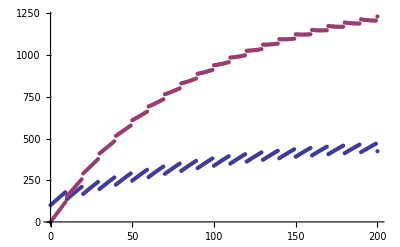

```mathematica
ListPlot[{p1, p2}]
```

```mathematica
Export["testtheoryc.dat", meantaba]
```

testtheoryc.dat